## Part 3.1.

```mathematica
Clear[σ,E1,E2,μ1,μ2,μ3,ϵ]
DSolve[σ'[t]+(E1+E2)/(μ1+μ2+μ3)σ[t]==(E1 E2)/(μ1+μ2+μ3)ϵ,σ[t],t]
```

{{σ[t]→(ⅇ^(-(E1 t)/(μ1+μ2+μ3)-(E2 t)/(μ1+μ2+μ3)+((E1+E2) t)/(μ1+μ2+μ3)) E1 E2 ϵ)/(E1+E2)+ⅇ^(-(E1 t)/(μ1+μ2+μ3)-(E2 t)/(μ1+μ2+μ3)) C[1]}}

## Part 3.2.

```mathematica
Clear[a,b,c,E1,E2,m1,m2,m3,σ,x]
a=(E1 m3+E2(m1+m2))/(2m3(m1+m2));b=(E1 E2)/(m3(m1+m2));c=(E1+E2)/((m1+m2)m3)σ;
DSolve[{x''[t]+2a x'[t]+b x[t]==c},x[t],t]
```

{{x[t]→(E1 σ+E2 σ)/(E1 E2)+ⅇ^(-(E2 t)/m3) C[1]+ⅇ^(-(E1 t)/(m1+m2)) C[2]}}

```mathematica
x[t_]=(E1 σ+E2 σ)/(E1 E2)-ⅇ^(-(E2 t)/m3)(k+(E1+E2)/(E1 E2)σ)+ⅇ^(-(E1 t)/(m1+m2)) k
```

ⅇ^(-(E1 t)/(m1+m2)) k+(E1 σ+E2 σ)/(E1 E2)-ⅇ^(-(E2 t)/m3) (k+((E1+E2) σ)/(E1 E2))

```mathematica
Simplify[x[0]]
```

0

```mathematica
Solve[x'[0]==0,k]
```

{{k→((E1+E2) (m1+m2) σ)/(E1 (-E2 m1-E2 m2+E1 m3))}}

## Part 3.3.

```mathematica
Clear[ϵ0,ω,ϕ0]
ϵ[t_]=ϵ0 Exp[I(ω t+ϕ0)];
lhs=Simplify[(m1+m2)m3 ϵ''[t]+(E1 m3+E2(m1+m2))ϵ'[t]+E1 E2 ϵ[t]]
```

ⅇ^(ⅈ (ϕ0+t ω)) ϵ0 (E1+ⅈ (m1+m2) ω) (E2+ⅈ m3 ω)

## Plots

### 4.1. Piecewise Stress

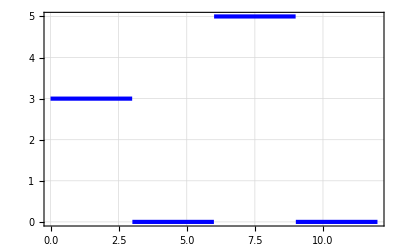

{{ϵ[t]→InterpolatingFunction[…][t]}}

```mathematica
E1=2.5;E2=3;
m1=1;m2=1;m3=1;
Clear[σ,ϵ,sol,t]
σ[t_]=Piecewise[
{{3,t<3},
{0,3<=t<6},
{5,6<=t<9},
{0,t>=9}}
];
Plot[σ[t],{t,0,12},PlotTheme->"Scientific",PlotStyle->Directive[Blue,Thickness[0.0075]],GridLines->Automatic]
sol=NDSolve[{(m1+m2)m3 ϵ''[t]+(E1 m3+E2(m1+m2))ϵ'[t]+E1 E2 ϵ[t]==(E1+E2)σ[t]+(m1+m2+m3)σ'[t],ϵ[0]==0,ϵ'[0]==0},ϵ[t],{t,0,12}]
```

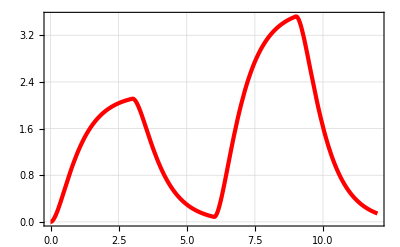

```mathematica
Plot[Evaluate[ϵ[t]/.sol],{t,0,12},PlotRange->All,PlotTheme->"Scientific",PlotStyle->Directive[Red,Thickness[0.0075]],GridLines->Automatic]
```

### 4.2. Piecewise Stretch

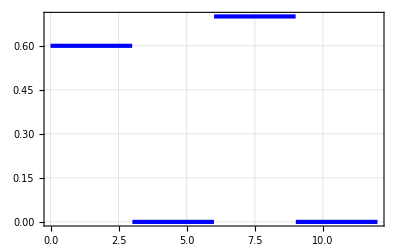

{{σ[t]→InterpolatingFunction[…][t]}}

```mathematica
E1=2.5;E2=3;
m1=1;m2=1;m3=1;
Clear[σ,ϵ,sol,t]
ϵ[t_]=Piecewise[
{{0.6,t<3},
{0,3<=t<6},
{0.7,6<=t<9},
{0,t>=9}}
];
Plot[ϵ[t],{t,0,12},PlotTheme->"Scientific",PlotStyle->Directive[Blue,Thickness[0.0075]],GridLines->Automatic]
sol=NDSolve[{(m1+m2)m3 ϵ''[t]+(E1 m3+E2(m1+m2))ϵ'[t]+E1 E2 ϵ[t]==(E1+E2)σ[t]+(m1+m2+m3)σ'[t],σ[0]==2},σ[t],{t,0,12}]
```

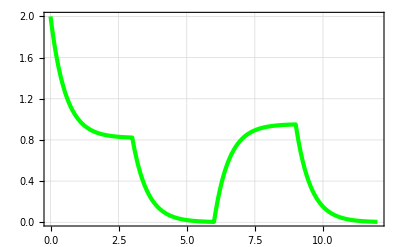

```mathematica
Plot[Evaluate[σ[t]/.sol],{t,0,12},PlotRange->All,PlotTheme->"Scientific",PlotStyle->Directive[Green,Thickness[0.0075]],GridLines->Automatic]
```

### 4.3. Harmonic Oscillations

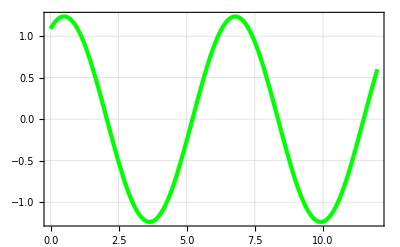

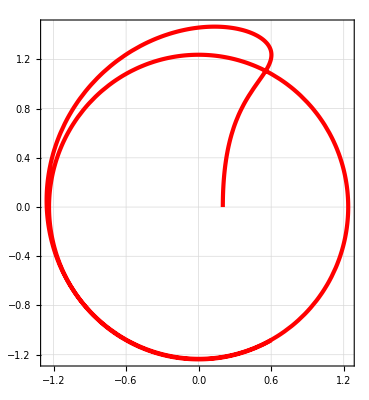

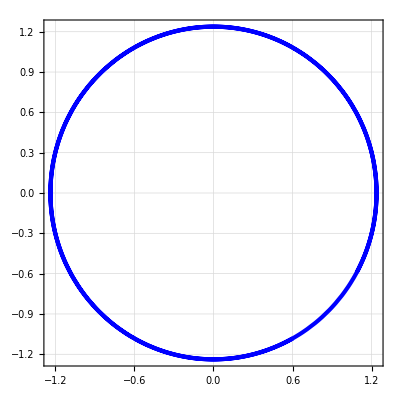

```mathematica
E1=2.5;E2=3;
m1=1;m2=1;m3=1;
ω=1;σ0=2;
Clear[σ,ϵ,sol,t]
σ[t_]=σ0 Exp[I ω t];
ϵ0=(Sqrt[(E1+E2)^2+ω^2(m1+m2+m3)^2]σ0)/Sqrt[(E1 E2-ω^2 m3(m1+m2))^2+(E1 m3+E2(m1+m2))^2 ω^2];
ϕ0=Arg[(((E1 E2-ω^2(m1+m2)m3)+(E1 m3+E2 (m1+m2))I ω)/((E1+E2)+(m1+m2+m3)I ω))^-1 σ0];

solwrong=NDSolve[{(m1+m2)m3 ϵ''[t]+(E1 m3+E2(m1+m2))ϵ'[t]+E1 E2 ϵ[t]==(E1+E2)σ[t]+(m1+m2+m3)σ'[t],ϵ[0]==0.2,ϵ'[0]==4I},ϵ[t],{t,0,12}];
solcorrect=NDSolve[{(m1+m2)m3 ϵ''[t]+(E1 m3+E2(m1+m2))ϵ'[t]+E1 E2 ϵ[t]==(E1+E2)σ[t]+(m1+m2+m3)σ'[t],ϵ[0]==ϵ0 Exp[I ϕ0],ϵ'[0]==ϵ0 ω I Exp[I ϕ0]},ϵ[t],{t,0,12}];
xs[t_]=Re[Evaluate[ϵ[t]/.solcorrect]];
ys[t_]=Im[Evaluate[ϵ[t]/.solcorrect]];
xsyswrong[t_]=Evaluate[{Re[ϵ[t]],Im[ϵ[t]]}/.solwrong];
xsyscorrect[t_]=Evaluate[{Re[ϵ[t]],Im[ϵ[t]]}/.solcorrect];
Plot[xs[t],{t,0,12},PlotRange->All,PlotTheme->"Scientific",PlotStyle->Directive[Green,Thickness[0.0075]],GridLines->Automatic]
ParametricPlot[xsyswrong[t],{t,0,12},PlotRange->All,PlotTheme->"Scientific",PlotStyle->Directive[Red,Thickness[0.0075]],GridLines->Automatic]
ParametricPlot[xsyscorrect[t],{t,0,12},PlotRange->All,PlotTheme->"Scientific",PlotStyle->Directive[Blue,Thickness[0.0075]],GridLines->Automatic]
```